Augustine Stav
Professor Onuttom Narayan
May 18, 2016

Phys 242 Homework 6

1.

```mathematica
sol1 = NRoots[x^7 + x^5 + 2x^3 + x^2 + 1 == 0, x]
```

x==-0.812432||x==-0.640787-1.07931 ⅈ||x==-0.640787+1.07931 ⅈ||x==0.254825-0.700968 ⅈ||x==0.254825+0.700968 ⅈ||x==0.792178-0.881387 ⅈ||x==0.792178+0.881387 ⅈ

2.

```mathematica
sol2 = NIntegrate[(HermiteH[4, x])^2  Exp[-x^2], {x, -Infinity,Infinity}]
```

680.622

3a.

```mathematica
sol3a = NDSolve[ {y''[x] -2x - y[x] -  3y'[x]==0, y'[2] == -1, y[2] ==1}, y, {x, 2,2.3} ]
```

{{y→InterpolatingFunction[{{2., 2.3}}, <>]}}

3b.

```mathematica
sol3b = y[2.2] /. sol3a[[1]]
```

0.851094

3c.

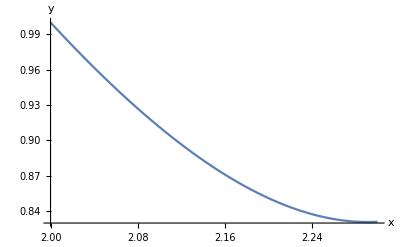

```mathematica
Plot[y[x] /. sol3a, {x, 2, 2.3}, AxesLabel -> {"x", " y" }]
```

4.

```mathematica
sol4 = Solve [ {4x +5 y == 5, 6x + 7y == 7}, {x, y} ]
```

{{x→0,y→1}}

5.

```mathematica
sol5 = Solve [ Sqrt[x+2]+4 == x, x]
```

{{x→7}}

Mathematica may convert the above to the polynomial equation x + 2 = (x-4)^2 = x^2 - 8x + 16 and choose the solution which solves the orginal problem (that with (x-4)^2 ≥ 0).

6.

```mathematica
sol6 = Limit[(Exp[x] - Exp[x-x^(-2)])^(-1), x -> Infinity]
```

0

7a.

```mathematica
xlist = Table[x, {x, 0, 10}]
```

{0,1,2,3,4,5,6,7,8,9,10}

7b.

```mathematica
ylist= xlist^2
```

{0,1,4,9,16,25,36,49,64,81,100}

7c.

```mathematica
xydata = Transpose[{xlist, ylist}]
```

{{0,0},{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100}}

7d.

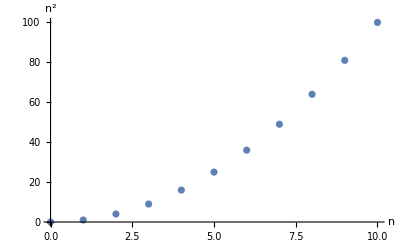

```mathematica
ListPlot[xydata, AxesLabel -> {"n", Superscript["n", "2"] }]
```

8.

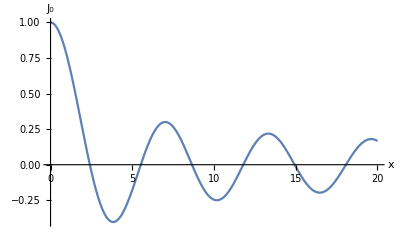

```mathematica
Plot[BesselJ[0,x], {x,0,20}, AxesLabel -> {"x", Subscript["J","0"] }]
```

```mathematica
sol8root1 = FindRoot[ BesselJ[0,x] == 0 , {x, 2.5} ]
```

{x→2.40483}

```mathematica
sol8root2 = FindRoot[ BesselJ[0,x] == 0 , {x, 5} ]
```

{x→5.52008}

```mathematica
sol8root3= FindRoot[ BesselJ[0,x] == 0 , {x, 9} ]
```

{x→8.65373}

```mathematica
sol8root4 = FindRoot[ BesselJ[0,x] == 0 , {x, 12} ]
```

{x→11.7915}

```mathematica
sol8root5 = FindRoot[ BesselJ[0,x] == 0 , {x, 15} ]
```

{x→14.9309}

9a.

```mathematica
f[x_] := λ*Sin[Pi x] ;
lya[l_, xinit_, n_, ndrop_] := (λ=l;xlist = Drop[NestList[f,xinit,n],ndrop+1];Apply[Plus,Log[Abs[f'[xlist]]]]/Length[xlist])

 lya[0.9 ,0.4 , 50000, 1000]
```

0.349229

9b.

```mathematica
λ = 9/10; x0=N[4/10, 1000];
N[sol9=Nest[f, x0, 5000], 6]
```

0.795585

```mathematica
Precision[sol9]
```

251.78

10.

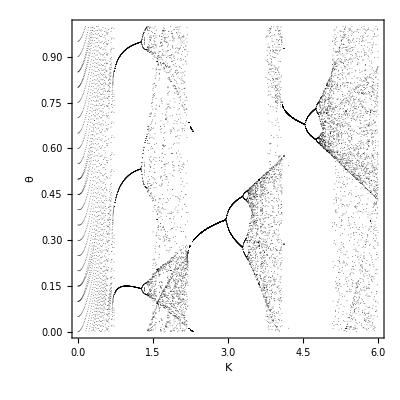

```mathematica
f[θ_] := Mod[θ+ Ω+K*Sin[2Pi θ]/(2Pi) ,1];
Ω = 0.65;
iterate[m_,n_] := Drop[NestList[f,0.1,n],m]
drawpt[y_] := Point[{K,y}]
graph[Kmin_, Kmax_,nK_,mdrop_,n_]:=Graphics[{PointSize[0.001],Table[Map[drawpt,iterate[mdrop,n]],{K,Kmin,Kmax,(Kmax-Kmin)/nK}]}]
Show[graph[0,6, 600, 75, 100], Axes->False,Frame->True,FrameLabel->{"K","θ"},PlotRange->{{0,6},{0,1}},AspectRatio->1]
```